```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/tbent/projects/codim1/notes

```mathematica
Needs["OrthogonalPolynomials`"]
```

OrthogonalPolynomials::usage: Please cite every usage of this package by the following two papers: 
\r
1. A.S. Cvetkovic, G.V. Milovanovic, The Mathematica Package ''OrthogonalPolynomials'', Facta Univ. Ser. Math. Inform. 19 (2004), 17-36.
\r
2. G.V. Milovanovic, A.S. Cvetkovic, Special classes of orthogonal polynomials and corresponding quadratures of Gaussian type, Math. Balkanica 26 (2012), 169-184.

```mathematica
n=4;
w[t_,x_]:=1/(1 - a*t);
mom=Integrate[t^k *w[t,a],{t,b,c}, Assumptions->{k≥0,Im[a]==0, a<1, a> -10^100}];
```

```mathematica
moments=Table[mom,{k,0,2 * n - 1}]
```

{ConditionalExpression[(Log[1-a b]-Log[1-a c])/a,0<b<c],ConditionalExpression[(-Beta[a b,2,0]+Beta[a c,2,0])/a^2,0<b<c],ConditionalExpression[(-Beta[a b,3,0]+Beta[a c,3,0])/a^3,0<b<c],ConditionalExpression[(-Beta[a b,4,0]+Beta[a c,4,0])/a^4,0<b<c],ConditionalExpression[(-Beta[a b,5,0]+Beta[a c,5,0])/a^5,0<b<c],ConditionalExpression[(-Beta[a b,6,0]+Beta[a c,6,0])/a^6,0<b<c],ConditionalExpression[(-Beta[a b,7,0]+Beta[a c,7,0])/a^7,0<b<c],ConditionalExpression[(-Beta[a b,8,0]+Beta[a c,8,0])/a^8,0<b<c]}

```mathematica
{alpha,beta}= aChebyshevAlgorithm[moments, Precision->2000,WorkingPrecision->2000];
```

```mathematica
parameters=aGaussianNodesWeights[n,alpha,beta,Precision->2000,
WorkingPrecision->2000];
```

$Aborted

```mathematica
{pts,wts}=aGaussianNodesWeights[n,{aLegendre},Precision->16, WorkingPrecision->50];
```

```mathematica
diff = 2 * parameters⟦1⟧ - 1 - pts;
```

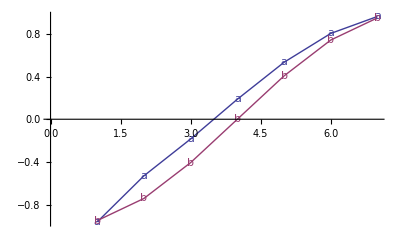

```mathematica
ListLinePlot[{2*parameters[[1]] - 1, pts},PlotMarkers->{"a","b"}]
```